```mathematica
ClearAll["Global`*"]
<<Utilities`CleanSlate`
CleanSlate[]
ClearInOut[]

pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]

Needs["VariationalMethods`"]
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 111 Kb

{Utilities`CleanSlate`,TriangleLink`,CompiledFunctionTools`,IPOPTLink`,VariationalMethods`,DocumentationSearch`,ResourceLocator`,System`,Global`,Graphics`Mesh`,Graphics`PolygonUtils`}

```mathematica
Clear[r]
r = { l Sin[ϕ[t]] + 3/4 l Sin[θ[t]] , - l Cos[ϕ[t]] - 3/4 l Cos[θ[t]] }
```

{3/4 l Sin[θ[t]]+l Sin[ϕ[t]],-3/4 l Cos[θ[t]]-l Cos[ϕ[t]]}

```mathematica
D[r, t]
```

{3/4 l Cos[θ[t]] θ'[t]+l Cos[ϕ[t]] ϕ'[t],3/4 l Sin[θ[t]] θ'[t]+l Sin[ϕ[t]] ϕ'[t]}

```mathematica
D[r, t] . D[r, t]
```

(3/4 l Cos[θ[t]] θ'[t]+l Cos[ϕ[t]] ϕ'[t])^2+(3/4 l Sin[θ[t]] θ'[t]+l Sin[ϕ[t]] ϕ'[t])^2

```mathematica
D[r, t] . D[r, t]  // Expand
```

9/16 l^2 Cos[θ[t]]^2 θ'[t]^2+9/16 l^2 Sin[θ[t]]^2 θ'[t]^2+3/2 l^2 Cos[θ[t]] Cos[ϕ[t]] θ'[t] ϕ'[t]+3/2 l^2 Sin[θ[t]] Sin[ϕ[t]] θ'[t] ϕ'[t]+l^2 Cos[ϕ[t]]^2 ϕ'[t]^2+l^2 Sin[ϕ[t]]^2 ϕ'[t]^2

```mathematica
D[r, t] . D[r, t]  // Expand  // Simplify
```

1/16 l^2 (9 θ'[t]^2+24 Cos[θ[t]-ϕ[t]] θ'[t] ϕ'[t]+16 ϕ'[t]^2)

```mathematica
Clear[T]
T = 
1/2 m ( D[r, t] . D[r, t]  // Expand  // Simplify  ) + 1/2(1/12 m ((3 l)/2)^2) θ'[t]^2
```

3/32 l^2 m θ'[t]^2+1/32 l^2 m (9 θ'[t]^2+24 Cos[θ[t]-ϕ[t]] θ'[t] ϕ'[t]+16 ϕ'[t]^2)

```mathematica
r
r[[2]]
```

{3/4 l Sin[θ[t]]+l Sin[ϕ[t]],-3/4 l Cos[θ[t]]-l Cos[ϕ[t]]}

-3/4 l Cos[θ[t]]-l Cos[ϕ[t]]

```mathematica
Clear[V]
V = - m g r[[2]]  // Expand // Simplify
```

1/4 g l m (3 Cos[θ[t]]+4 Cos[ϕ[t]])

```mathematica
Clear[ℒ]
ℒ = T - V  ;
ℒ // pdConv
```

-1/4 g l m (3 cos(θ(t))+4 cos(ϕ(t)))+1/32 l^2 m (24 (∂θ(t))/(∂t) (∂ϕ(t))/(∂t) cos(θ(t)-ϕ(t))+9 ((∂θ(t))/(∂t))^2+16 ((∂ϕ(t))/(∂t))^2)+3/32 l^2 m ((∂θ(t))/(∂t))^2

```mathematica
Clear[q]
q = { θ[t] , ϕ[t] }
```

{θ[t],ϕ[t]}

```mathematica
D[ D[ ℒ , D[q[[1]], t] ], t ]  - D[ ℒ , q[[1]] ]  // Expand  // Simplify 
D[ D[ ℒ , D[q[[1]], t] ], t ]  - D[ ℒ , q[[2]] ]  // Expand // Simplify
```

3/4 l m (-g Sin[θ[t]]+l Sin[θ[t]-ϕ[t]] ϕ'[t]^2+l θ''[t]+l Cos[θ[t]-ϕ[t]] ϕ''[t])

1/4 l m (-4 g Sin[ϕ[t]]-6 l Sin[θ[t]-ϕ[t]] θ'[t] ϕ'[t]+3 l Sin[θ[t]-ϕ[t]] ϕ'[t]^2+3 l θ''[t]+3 l Cos[θ[t]-ϕ[t]] ϕ''[t])

```mathematica
Table[
D[ D[ ℒ , D[q[[i]], t] ], t ]  - D[ ℒ , q[[i]] ] , 
{ i, 1, 2 } ]  // Expand  // Simplify // TableForm
```

3/4 l m (-g Sin[θ[t]]+l Sin[θ[t]-ϕ[t]] ϕ'[t]^2+l θ''[t]+l Cos[θ[t]-ϕ[t]] ϕ''[t])
1/4 l m (-4 g Sin[ϕ[t]]-3 l Sin[θ[t]-ϕ[t]] θ'[t]^2+3 l Cos[θ[t]-ϕ[t]] θ''[t]+4 l ϕ''[t])

```mathematica
Clear[eqs]
eqs = 
EulerEquations[ ℒ , q, t ] ;
eqs // TableForm
```

-3/4 l m (-g Sin[θ[t]]+l Sin[θ[t]-ϕ[t]] ϕ'[t]^2+l θ''[t]+l Cos[θ[t]-ϕ[t]] ϕ''[t])==0
1/4 l m (4 g Sin[ϕ[t]]+3 l Sin[θ[t]-ϕ[t]] θ'[t]^2-3 l Cos[θ[t]-ϕ[t]] θ''[t]-4 l ϕ''[t])==0

```mathematica
Clear[parameters]
parameters = { 
m -> 10 , 
l-> 1 , 
g -> 9.8 
} ; 
parameters // TableForm
```

m→10
l→1
g→9.8

```mathematica
eqs /. parameters  // Expand // TableForm
```

73.5 Sin[θ[t]]-15/2 Sin[θ[t]-ϕ[t]] ϕ'[t]^2-(15 θ''[t])/2-15/2 Cos[θ[t]-ϕ[t]] ϕ''[t]==0
98. Sin[ϕ[t]]+15/2 Sin[θ[t]-ϕ[t]] θ'[t]^2-15/2 Cos[θ[t]-ϕ[t]] θ''[t]-10 ϕ''[t]==0

```mathematica
Clear[ics]
ics = { 
θ[0] == 0.1 , 
θ'[0] == 0 , 
ϕ[0] == 0 , 
ϕ'[0] == 0.2 } ;
ics // TableForm
```

θ[0]==0.1
θ'[0]==0
ϕ[0]==0
ϕ'[0]==0.2

```mathematica
Clear[solution]
solution[t_] = 
First[ NDSolve[ Union[ eqs /. parameters , ics ] , q , { t, 0, 300 } ]  ]
```

{θ[t]→InterpolatingFunction[{{0., 300.}}, <>][t],ϕ[t]→InterpolatingFunction[{{0., 300.}}, <>][t]}

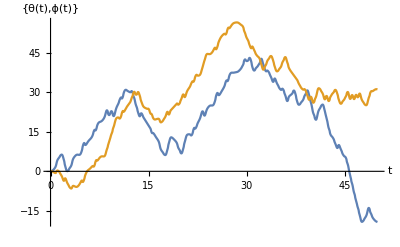

```mathematica
Plot[ Evaluate[ q/. solution[t] ] , { t, 0, 50 } , AxesLabel-> { t , q }  ]
```

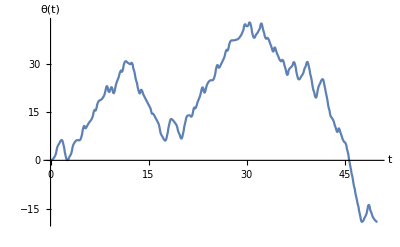

```mathematica
Plot[ q[[1]] /. solution[t] , { t, 0, 50 }, AxesLabel-> { t , q[[1]] }  ]
```

```mathematica
Animate[ 
ParametricPlot[ { solution[t][[1,2]] , solution'[t][[1,2]] } , { t , 0, tmax } , AxesLabel-> { q[[1]] , D[q[[1]], t] } ]  ,
{ tmax , 1 ,50 , 0.5  } ]
```

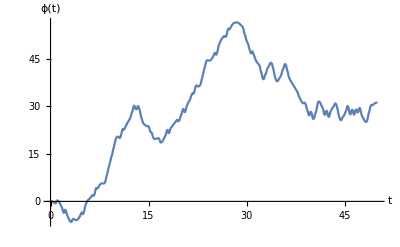

```mathematica
Plot[ q[[2]] /. solution[t] , { t, 0, 50 }, AxesLabel-> { t , q[[2]] } ]
```

```mathematica
Animate[ 
ParametricPlot[ { solution[t][[2,2]] , solution'[t][[2,2]] } , { t , 0, tmax } , AxesLabel-> { q[[2]] , D[q[[2]], t] } ]  ,
{ tmax , 1 ,50 , 0.5  } ]
```